We have two equations derived from the Markov model in the paper. The first is that the sum of the state number i (i.e. number of valid pages in a block) times the fraction of blocks in state i gives us the mean number of valid pages in a block, N_p/α :

```mathematica
eq1 = Sum[k,{i,Subscript[X, 0],Subscript[N, p]}] == Subscript[N, p]/α
```

k (N_p-X_0+1)==N_p/α

```mathematica
The second is that the state probabilities (or equivalently, fraction of blocks in state i) sum to 1. (ignore the subscript on Subscript[k, i]- it's to force non-evaluated output).
```

```mathematica
Sum[Subscript[f, i],{i,Subscript[X, 0],Subscript[N, p]}] == Sum[Subscript[k, i]/i,{i,Subscript[X, 0],Subscript[N, p]}] == 1
```

∑_(i=X_0)^N_p f_i==∑_(i=X_0)^N_p k_i/i==1

```mathematica
The exact solution to that summation is quite ugly, so we approximate it with an integral with continuity correction:
```

```mathematica
eq2 = Integrate[k/i, {i, Subscript[X, 0]-1/2,Subscript[N, p]+1/2}, Assumptions->{k>0,1 < Subscript[X, 0]<Subscript[N, p]}] == 1
```

k log((2 N_p+1)/(2 X_0-1))==1

```mathematica
Now we can get a solution for Subscript[X, 0], the lowest-numbered state with non-negligible occupation (see the graph in the paper for details):
```

```mathematica
soln1 = Solve[eq1, k][[1]]
```

{k→N_p/(α (N_p-X_0+1))}

```mathematica
soln = Solve[eq2 /. soln1, Subscript[X, 0],InverseFunctions->True][[1]]
```

{X_0→(α-2 N_p W(-(α (2 N_p+1) ⅇ^(α/(2 N_p)-(α (N_p+1))/N_p))/(2 N_p)))/(2 α)}

```mathematica
And we can calculate A by observing that blocks have Subscript[X, 0]-1 valid pages when selected for cleaning:
```

```mathematica
Subscript[A, gr][α_] = FullSimplify[Subscript[N, p]/(Subscript[N, p]-(Subscript[X, 0]-1)) /. soln]
```

(2 α N_p)/(α+2 N_p (α+W(-(α (2 N_p+1) ⅇ^(-α-α/(2 N_p)))/(2 N_p))))

```mathematica
Here we compare LRU cleaning to Greedy cleaning with Subscript[N, p]= 16, 64:
```

```mathematica
Subscript[A, lru][α_] = α/(α + ProductLog[(-Exp[-α])*α])
```

α/(α+W(-ⅇ^-α α))

```mathematica
Needs["PlotLegends`"]
```

```mathematica
Plot[{Subscript[A, lru][α],Subscript[A, gr][α]/. Subscript[N, p]->64, Subscript[A, gr][α]/.Subscript[N, p]->16},{α,1.03,1.2},AxesOrigin->{1,0}, PlotStyle-> Thick,PlotLegend->{"LRU", "N_p=64", "N_p=16"},TicksStyle->Directive[14]]
```

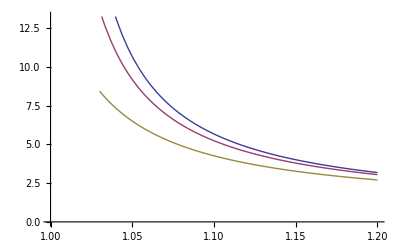

```mathematica
With a change of variable we can simplify Subscript[A, gr][α] quite a bit:
```

```mathematica
eq3 = α1 == (1 + 1/(2*Subscript[N, p]))*α
```

α1==α (1+1/(2 N_p))

```mathematica
soln = Solve[eq3,α][[1]]
```

{α→(2 α1 N_p)/(1+2 N_p)}

```mathematica
expr = FullSimplify[Subscript[A, gr][α]/.soln]
```

(2 α1 N_p)/((2 N_p+1) (α1+W(-ⅇ^-α1 α1)))

```mathematica
At which point it starts looking very familiar.
```

```mathematica
expr2 = expr /. {α_/(α_+ProductLog[-Exp[-α_]*α_]) -> LRU[α]}
```

(2 LRU(α1) N_p)/(2 N_p+1)

```mathematica
LRU[α1]*Apart[expr2/LRU[α1]] == LRU[α1]*eq3[[2]][[2]]
```

LRU[α1] (1-1/(1+2 N_p))==LRU[α1] (1+1/(2 N_p))

```mathematica
In other words:
```

```mathematica
Subscript[A, greedy][α] == (1+1/(2*Subscript[N, p]))*Subscript[A, LRU][α*(1+1/(2*Subscript[N, p]))]
```

A_greedy[α]==(1+1/(2 N_p)) A_LRU[α (1+1/(2 N_p))]